### Preliminary

```mathematica
$HistoryLength=4;
```

```mathematica
ma=6.015122 ;
mi=170.936323 ;
μ=Sqrt[ma/mi];
```

Let’s write a module for plotting from a file

```mathematica
MakePlot[file_,xcol_,ycols_,prange_,flabel_,otheroptions_]:=Module[
{AllData,PlotData,Ncols},
AllData=Transpose[Import[file]];
Ncols=Dimensions[AllData][[1]];
PlotData=Table[Transpose[{AllData[[xcol]],AllData[[ycol]]}],{ycol,ycols}];
ListPlot[PlotData,otheroptions, Joined->True,Frame->True,PlotTheme->None,LabelStyle->{16},PlotStyle->{Black,Red,Green,Blue,Purple},GridLinesStyle->Thin,PlotRange->prange,FrameLabel->flabel]
]
```

```mathematica
MakeData[file_,xcol_,ycols_]:=Module[
{AllData,PlotData,Ncols},
AllData=Transpose[Import[file]];
Ncols=Dimensions[AllData][[1]];
If[Length[ycols]>1,
PlotData=Table[Transpose[{AllData[[xcol]],AllData[[ycol]]}],{ycol,ycols}],
PlotData=Transpose[{AllData[[xcol]],AllData[[ycols[[1]]]]}]]
]
```

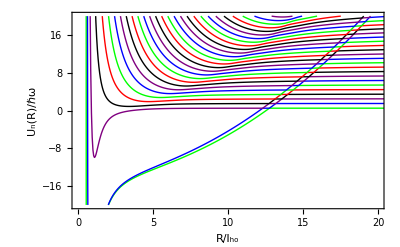

```mathematica
MakePlot["/Users/niravmehta/Documents/GitHub/AtomIon1D/AdiabaticEnergies.dat",1,Table[n,{n,2,40}],{{0,20},{-20,20}},{"R/l_ho","U_n(R)/ℏω"},{}]
```

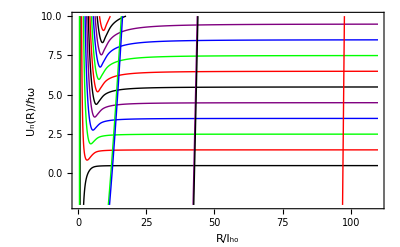

```mathematica
MakePlot["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/3bs/DiabaticEnergies.dat",1,Table[n,{n,2,18}],{{0,110},{-2,10}},{"R/l_ho","U_n(R)/ℏω"},{}]
```

```mathematica
RawDiabaticCurves=Transpose[Drop[Import["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/2bs/twoopenchannels/DiabaticEnergies.dat"],1]];
```

```mathematica
RawDiabaticCurves[[2]];
```

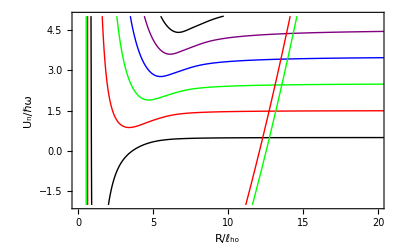

```mathematica
ListPlot[Table[Transpose[{RawDiabaticCurves[[1]],RawDiabaticCurves[[ycol]]}],{ycol,2,41}],PlotTheme->None,Joined->True,PlotStyle->{Black,Red,Green,Blue,Purple},PlotRange->{{0,20},{-2,5}},Frame->True,LabelStyle->{Black,16},FrameLabel->{"R/ℓ_ho","U_n/ℏω"}]
```

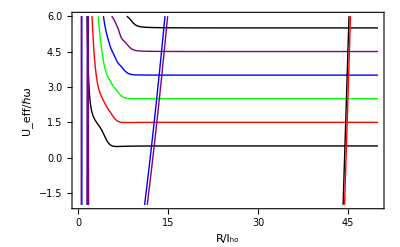

```mathematica
MakePlot["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/2bs/twoopenchannels/QuickEffV.dat",1,{2,3,4,5,6,7,8,9,10,11,12,13},{{0,50},{-2,6}},{"R/l_ho","U_eff/ℏω"},{}]
```

### Some data

```mathematica
onechan3bsplusparity=MakeData["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/3bs/oneopenchannel/plusparity/Save1.dat",1,{3}];
onechan3bsnegparity=MakeData["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/3bs/oneopenchannel/negparity/Save1.dat",1,{3}];
Z1onechan3bsplusparity=MakeData["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/3bs/oneopenchannel/plusparity/ZoomSave1.dat",1,{3}];
Z1onechan3bsnegparity=MakeData["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/3bs/oneopenchannel/negparity/ZoomSave1.dat",1,{3}];
Z2onechan3bsplusparity=MakeData["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/3bs/oneopenchannel/plusparity/ZoomSave2.dat",1,{3}];
Z2onechan3bsnegparity=MakeData["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/3bs/oneopenchannel/negparity/ZoomSave2.dat",1,{3}];
totalonechannel3bs=Transpose[{Transpose[onechan3bsnegparity][[1]],Transpose[onechan3bsplusparity][[2]]}];
ListPlot[totalonechannel3bs,PlotTheme->None,Joined->True];
```

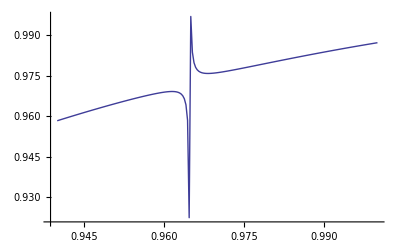

```mathematica
ListPlot[Z1onechan3bsplusparity,Joined->True,PlotTheme->None]
```

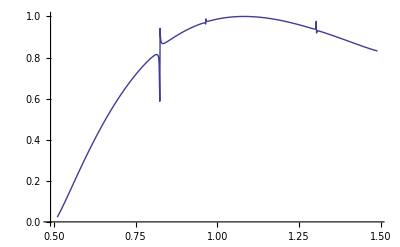

```mathematica
ListPlot[SortBy[Join[{onechan3bsplusparity,Z1onechan3bsplusparity,Z2onechan3bsplusparity}][[1]],First],Joined->True,PlotTheme->None]
```

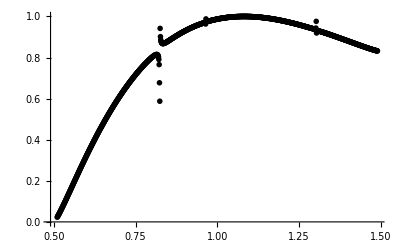

```mathematica
ListPlot[[[1]]]
```

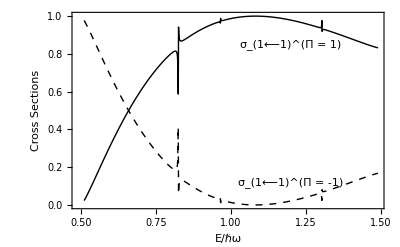

```mathematica
ponechan=ListPlot[{SortBy[Join[{onechan3bsplusparity,Z1onechan3bsplusparity,Z2onechan3bsplusparity}][[1]],First],SortBy[Join[{onechan3bsnegparity,Z1onechan3bsnegparity,Z2onechan3bsnegparity}][[1]],First]},FrameLabel->{"E/ℏω","Cross Sections"},LabelStyle->{Black,18},Frame->True,PlotTheme->None,PlotStyle->{{Black},{Black,Dashed}},Joined->True,Epilog->{Style[Text["σ_(1⟵1)^(Π = 1)",{1.2,0.85}],{Black,18}],Style[Text["σ_(1⟵1)^(Π = -1)",{1.2,0.12}],{Black,18}]}]
```

```mathematica
twochan2bsplusparity=MakeData["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/2bs/twoopenchannels/plusparity/Observables1.dat",1,{3,4,5,6}];
twochan2bsnegparity=MakeData["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/2bs/twoopenchannels/negparity/Observables-1.dat",1,{3,4,5,6}];
```

```mathematica
Dimensions[twochan2bsplusparity]
```

{4,4000,2}

```mathematica
totaltwochannel2bs11=Transpose[{Transpose[twochan2bsplusparity[[1]]][[1]],Transpose[twochan2bsplusparity[[1]]][[2]]+Transpose[twochan2bsnegparity[[1]]][[2]]}];
totaltwochannel2bs22=Transpose[{Transpose[twochan2bsplusparity[[4]]][[1]],Transpose[twochan2bsplusparity[[4]]][[2]]+Transpose[twochan2bsnegparity[[4]]][[2]]}];
totaltwochannel2bs12=Transpose[{Transpose[twochan2bsplusparity[[3]]][[1]],Transpose[twochan2bsplusparity[[3]]][[2]]+Transpose[twochan2bsnegparity[[3]]][[2]]}];
totaltwochannel2bs21=Transpose[{Transpose[twochan2bsplusparity[[2]]][[1]],Transpose[twochan2bsplusparity[[2]]][[2]]+Transpose[twochan2bsnegparity[[2]]][[2]]}];
```

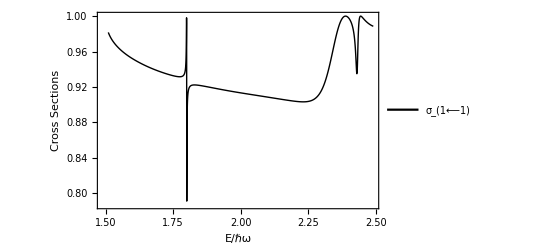

```mathematica
ptwochanelastic=ListPlot[Join[{totaltwochannel2bs11}],PlotLegends->Placed[{Style["σ_(1⟵1)",12],Style["σ_(2⟵1)",12]},{.8,.3}],
FrameLabel->{"E/ℏω","Cross Sections"},LabelStyle->{Black,18},Frame->True,PlotTheme->None,PlotStyle->{{Black},{Black,Dashed},{Red},{Red,Dashed}},Joined->True,ImageSize->{400,300}(*,Epilog->{
Style[Text["σ_(1⟵1)^(Π = +1)",{1.67,0.87}],{Black,18}],Style[Text["σ_(1⟵1)^(Π = -1)",{1.65,0.2}],{Red,18}],
Style[Arrow[{{1.6,.15},{1.7,0.01}}],{Red,Dashed}],
Style[Text["σ_(2⟵1)^(Π = 1)",{1.95,0.11}],{Green,18}]
}*)]
```

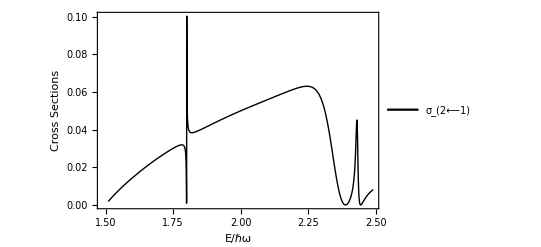

```mathematica
ptwochanelastic=ListPlot[Join[{totaltwochannel2bs21}],PlotLegends->Placed[{Style["σ_(2⟵1)",12]},{.8,.8}],
FrameLabel->{"E/ℏω","Cross Sections"},LabelStyle->{Black,18},Frame->True,PlotTheme->None,PlotStyle->{{Black},{Black,Dashed},{Red},{Red,Dashed}},Joined->True,ImageSize->{400,300}(*,Epilog->{
Style[Text["σ_(1⟵1)^(Π = +1)",{1.67,0.87}],{Black,18}],Style[Text["σ_(1⟵1)^(Π = -1)",{1.65,0.2}],{Red,18}],
Style[Arrow[{{1.6,.15},{1.7,0.01}}],{Red,Dashed}],
Style[Text["σ_(2⟵1)^(Π = 1)",{1.95,0.11}],{Green,18}]
}*)]
```

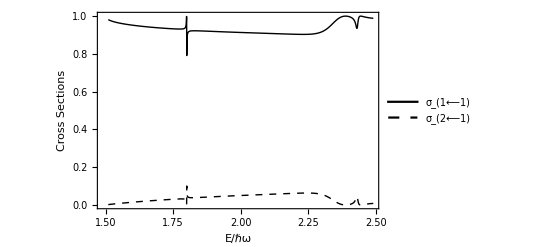

```mathematica
ptwochanelastic=ListPlot[Join[{totaltwochannel2bs11},{totaltwochannel2bs21}],PlotLegends->Placed[{Style["σ_(1⟵1)",12],Style["σ_(2⟵1)",12]},{.8,.3}],
FrameLabel->{"E/ℏω","Cross Sections"},LabelStyle->{Black,18},Frame->True,PlotTheme->None,PlotStyle->{{Black},{Black,Dashed},{Red},{Red,Dashed}},Joined->True,ImageSize->{400,300}(*,Epilog->{
Style[Text["σ_(1⟵1)^(Π = +1)",{1.67,0.87}],{Black,18}],Style[Text["σ_(1⟵1)^(Π = -1)",{1.65,0.2}],{Red,18}],
Style[Arrow[{{1.6,.15},{1.7,0.01}}],{Red,Dashed}],
Style[Text["σ_(2⟵1)^(Π = 1)",{1.95,0.11}],{Green,18}]
}*)]
```

```mathematica
twochan2bsplusparity=MakeData["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/2bs/twoopenchannels/plusparity/Smatrix1.dat",1,{2,3,4,5}];
twochan2bsnegparity=MakeData["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/2bs/twoopenchannels/negparity/Smatrix-1.dat",1,{2,3,4,5}];
totaltwochannel2bs11=Transpose[{Transpose[twochan2bsplusparity[[1]]][[1]],(Transpose[twochan2bsplusparity[[1]]][[2]]+Transpose[twochan2bsnegparity[[1]]][[2]])/2}];
totaltwochannel2bs22=Transpose[{Transpose[twochan2bsplusparity[[4]]][[1]],(Transpose[twochan2bsplusparity[[4]]][[2]]+Transpose[twochan2bsnegparity[[4]]][[2]])/2}];
totaltwochannel2bs12=Transpose[{Transpose[twochan2bsplusparity[[3]]][[1]],(Transpose[twochan2bsplusparity[[3]]][[2]]+Transpose[twochan2bsnegparity[[3]]][[2]])/2}];
totaltwochannel2bs21=Transpose[{Transpose[twochan2bsplusparity[[2]]][[1]],(Transpose[twochan2bsplusparity[[2]]][[2]]+Transpose[twochan2bsnegparity[[2]]][[2]])/2}];
```

```mathematica
ptwochanelastic=ListPlot[Join[{totaltwochannel2bs11},{totaltwochannel2bs21}],PlotLegends->Placed[{Style["P_(1⟵1)",12],Style["P_(2⟵1)",12]},{1,.5}],
FrameLabel->{"E/ℏω","Probability"},LabelStyle->{Black,18},Frame->True,PlotTheme->None,PlotStyle->{{Black},{Black,Dashed},{Red},{Red,Dashed}},Joined->True,ImageSize->{600,400},PlotRange->{0,1}(*,Epilog->{
Style[Text["σ_(1⟵1)^(Π = +1)",{1.67,0.87}],{Black,18}],Style[Text["σ_(1⟵1)^(Π = -1)",{1.65,0.2}],{Red,18}],
Style[Arrow[{{1.6,.15},{1.7,0.01}}],{Red,Dashed}],
Style[Text["σ_(2⟵1)^(Π = 1)",{1.95,0.11}],{Green,18}]
}*)]
```

-Graphics-

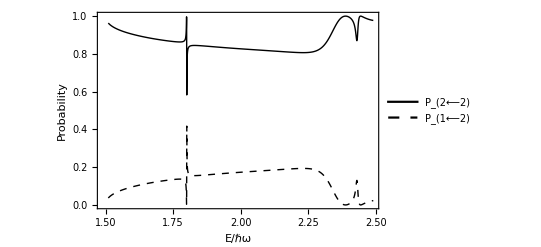

```mathematica
ptwochanelastic=ListPlot[Join[{totaltwochannel2bs22},{totaltwochannel2bs12}],PlotLegends->Placed[{Style["P_(2⟵2)",12],Style["P_(1⟵2)",12]},{0.8,.5}],
FrameLabel->{"E/ℏω","Probability"},LabelStyle->{Black,18},Frame->True,PlotTheme->None,PlotStyle->{{Black},{Black,Dashed},{Red},{Red,Dashed}},Joined->True,ImageSize->{400,300},PlotRange->{0,1}(*,Epilog->{
Style[Text["σ_(1⟵1)^(Π = +1)",{1.67,0.87}],{Black,18}],Style[Text["σ_(1⟵1)^(Π = -1)",{1.65,0.2}],{Red,18}],
Style[Arrow[{{1.6,.15},{1.7,0.01}}],{Red,Dashed}],
Style[Text["σ_(2⟵1)^(Π = 1)",{1.95,0.11}],{Green,18}]
}*)]
```

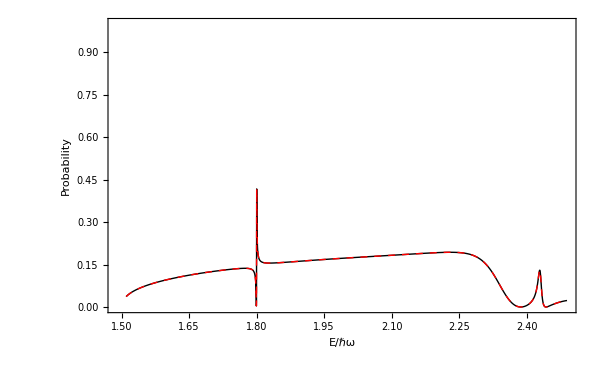

```mathematica
ptwochanelastic=ListPlot[Join[{totaltwochannel2bs12},{totaltwochannel2bs21}],(*PlotLegends->Placed[{Style["P_(1⟵1)",12],Style["P_(2⟵1)",12]},{1,.5}],*)
FrameLabel->{"E/ℏω","Probability"},LabelStyle->{Black,18},Frame->True,PlotTheme->None,PlotStyle->{{Black},{Red,Dashed},{Red},{Red,Dashed}},Joined->True,ImageSize->{600,400},PlotRange->{0,1}(*,Epilog->{
Style[Text["σ_(1⟵1)^(Π = +1)",{1.67,0.87}],{Black,18}],Style[Text["σ_(1⟵1)^(Π = -1)",{1.65,0.2}],{Red,18}],
Style[Arrow[{{1.6,.15},{1.7,0.01}}],{Red,Dashed}],
Style[Text["σ_(2⟵1)^(Π = 1)",{1.95,0.11}],{Green,18}]
}*)]
```

```mathematica
ptwochanelastic=ListPlot[Join[{twochan2bsplusparity[[1]]},{twochan2bsnegparity[[1]]},{twochan2bsplusparity[[4]]},{twochan2bsnegparity[[4]]}],PlotLegends->Placed[{Style["σ_(1⟵1)^(Π = +1)",12],Style["σ_(1⟵1)^(Π = -1)",12],Style["σ_(2⟵2)^(Π = 1)",12],Style["σ_(2⟵2)^(Π = -1)",12]},{1,.5}],
FrameLabel->{"E/ℏω","Cross Sections"},LabelStyle->{Black,18},Frame->True,PlotTheme->None,PlotStyle->{{Black},{Black,Dashed},{Red},{Red,Dashed}},Joined->True,ImageSize->{600,400}(*,Epilog->{
Style[Text["σ_(1⟵1)^(Π = +1)",{1.67,0.87}],{Black,18}],Style[Text["σ_(1⟵1)^(Π = -1)",{1.65,0.2}],{Red,18}],
Style[Arrow[{{1.6,.15},{1.7,0.01}}],{Red,Dashed}],
Style[Text["σ_(2⟵1)^(Π = 1)",{1.95,0.11}],{Green,18}]
}*)]
```

### Three bound states

#### two open channels

```mathematica
twochan3bsplusparity=MakeData["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/3bs/twoopenchannels/plusparity/Observables1.dat",1,{3,4,5,6}];
twochan3bsnegparity=MakeData["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/3bs/twoopenchannels/negparity/Observables-1.dat",1,{3,4,5,6}];
```

```mathematica
Stwochan3bsplusparity=MakeData["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/3bs/twoopenchannels/plusparity/Smatrix1.dat",1,{2,3,4,5}];
Stwochan3bsnegparity=MakeData["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/3bs/twoopenchannels/negparity/Smatrix-1.dat",1,{2,3,4,5}];
Stotaltwochannel3bs11=Transpose[{Transpose[Stwochan3bsplusparity[[1]]][[1]],(Transpose[Stwochan3bsplusparity[[1]]][[2]]+Transpose[Stwochan3bsnegparity[[1]]][[2]])/2}];
Stotaltwochannel3bs22=Transpose[{Transpose[Stwochan3bsplusparity[[4]]][[1]],(Transpose[Stwochan3bsplusparity[[4]]][[2]]+Transpose[Stwochan3bsnegparity[[4]]][[2]])/2}];
Stotaltwochannel3bs12=Transpose[{Transpose[Stwochan3bsplusparity[[3]]][[1]],(Transpose[Stwochan3bsplusparity[[3]]][[2]]+Transpose[Stwochan3bsnegparity[[3]]][[2]])/2}];
Stotaltwochannel3bs21=Transpose[{Transpose[Stwochan3bsplusparity[[2]]][[1]],(Transpose[Stwochan3bsplusparity[[2]]][[2]]+Transpose[Stwochan3bsnegparity[[2]]][[2]])/2}];
```

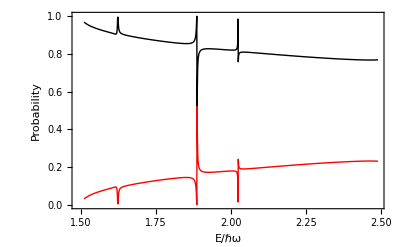

```mathematica
ptwochan3bsn1=ListPlot[Join[{Stotaltwochannel3bs11},{Stotaltwochannel3bs21}],(*PlotLegends->Placed[{Style["P_(1⟵1)",12],Style["P_(2⟵1)",12]},{0.8,.5}],*)
FrameLabel->{"E/ℏω","Probability"},LabelStyle->{Black,18},Frame->True,PlotTheme->None,PlotStyle->{{Black},{Red},{Green}},Joined->True,ImageSize->{400,300},PlotRange->{0,1}(*,Epilog->{
Style[Text["σ_(1⟵1)^(Π = +1)",{1.67,0.87}],{Black,18}],Style[Text["σ_(1⟵1)^(Π = -1)",{1.65,0.2}],{Red,18}],
Style[Arrow[{{1.6,.15},{1.7,0.01}}],{Red,Dashed}],
Style[Text["σ_(2⟵1)^(Π = 1)",{1.95,0.11}],{Green,18}]
}*)]
```

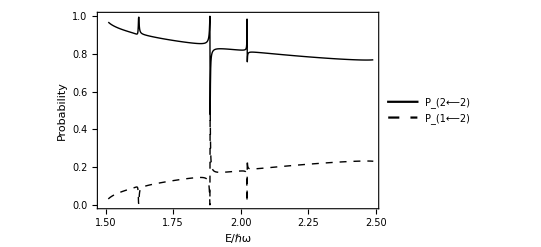
```mathematica
-Graphics-
-Graphics-
```

#### three open channels

```mathematica
threechan3bsplusparity=MakeData["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/3bs/threeopenchannels/plusparity/Observables1.dat",1,1+{2,3,4,5,6,7,8,9,10}];
threechan3bsnegparity=MakeData["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/3bs/threeopenchannels/negparity/Observables-1.dat",1,1+{2,3,4,5,6,7,8,9,10}];
Sthreechan3bsplusparity=MakeData["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/3bs/threeopenchannels/plusparity/Smatrix1.dat",1,{2,3,4,5,6,7,8,9,10}];
Sthreechan3bsnegparity=MakeData["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/3bs/threeopenchannels/negparity/Smatrix-1.dat",1,{2,3,4,5,6,7,8,9,10}];
Stotalthreechannel3bs11=Transpose[{Transpose[Sthreechan3bsplusparity[[1]]][[1]],(Transpose[Sthreechan3bsplusparity[[1]]][[2]]+Transpose[Sthreechan3bsnegparity[[1]]][[2]])/2}];
Stotalthreechannel3bs21=Transpose[{Transpose[Sthreechan3bsplusparity[[2]]][[1]],(Transpose[Sthreechan3bsplusparity[[2]]][[2]]+Transpose[Sthreechan3bsnegparity[[2]]][[2]])/2}];
Stotalthreechannel3bs31=Transpose[{Transpose[Sthreechan3bsplusparity[[3]]][[1]],(Transpose[Sthreechan3bsplusparity[[3]]][[2]]+Transpose[Sthreechan3bsnegparity[[3]]][[2]])/2}];
Stotalthreechannel3bs12=Transpose[{Transpose[Sthreechan3bsplusparity[[4]]][[1]],(Transpose[Sthreechan3bsplusparity[[4]]][[2]]+Transpose[Sthreechan3bsnegparity[[4]]][[2]])/2}];
Stotalthreechannel3bs22=Transpose[{Transpose[Sthreechan3bsplusparity[[5]]][[1]],(Transpose[Sthreechan3bsplusparity[[5]]][[2]]+Transpose[Sthreechan3bsnegparity[[5]]][[2]])/2}];
Stotalthreechannel3bs32=Transpose[{Transpose[Sthreechan3bsplusparity[[6]]][[1]],(Transpose[Sthreechan3bsplusparity[[6]]][[2]]+Transpose[Sthreechan3bsnegparity[[6]]][[2]])/2}];
Stotalthreechannel3bs13=Transpose[{Transpose[Sthreechan3bsplusparity[[7]]][[1]],(Transpose[Sthreechan3bsplusparity[[7]]][[2]]+Transpose[Sthreechan3bsnegparity[[7]]][[2]])/2}];
Stotalthreechannel3bs23=Transpose[{Transpose[Sthreechan3bsplusparity[[8]]][[1]],(Transpose[Sthreechan3bsplusparity[[8]]][[2]]+Transpose[Sthreechan3bsnegparity[[8]]][[2]])/2}];
Stotalthreechannel3bs33=Transpose[{Transpose[Sthreechan3bsplusparity[[9]]][[1]],(Transpose[Sthreechan3bsplusparity[[9]]][[2]]+Transpose[Sthreechan3bsnegparity[[9]]][[2]])/2}];
```

```mathematica
Dimensions[Sthreechan3bsplusparity]
```

{9,2000,2}

```mathematica
pthreechan3bsn1=ListPlot[Join[{Stotalthreechannel3bs11,Stotalthreechannel3bs21,Stotalthreechannel3bs31}](*,PlotLegends->Placed[{Style["P_(2⟵2)",12],Style["P_(1⟵2)",12]},{0.8,.5}]*),PlotLegends->Placed[{Style["P_(1⟵1)",12],Style["P_(2⟵1)",12],Style["P_(3⟵1)",12]},{1,.45}],
FrameLabel->{"E/ℏω","Probability"},LabelStyle->{Black,18},Frame->True,PlotTheme->None,PlotStyle->{{Black},{Red},{Green},{Red,Dashed}},Joined->True,ImageSize->{400,300},PlotRange->{0,1}(*,Epilog->{
Style[Text["σ_(1⟵1)^(Π = +1)",{1.67,0.87}],{Black,18}],Style[Text["σ_(1⟵1)^(Π = -1)",{1.65,0.2}],{Red,18}],
Style[Arrow[{{1.6,.15},{1.7,0.01}}],{Red,Dashed}],
Style[Text["σ_(2⟵1)^(Π = 1)",{1.95,0.11}],{Green,18}]
}*)]
```

-Graphics-

```mathematica
Show[{ptwochan3bsn1,pthreechan3bsn1},PlotRange->All]
```

-Graphics-

### Plots from the K-matrix

Let’s see if we can make all of the plots above from the K-matrix for the positive parity calculations, using the fact that K_(Π=-1)=-K_(Π=1)^-1.

```mathematica
twochan2bsKmat0Raw=Transpose[Import["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/2bs/twoopenchannels/plusparity/Kmatrix1.dat"]];
```

```mathematica
Dimensions[Transpose[twochan2bsKmat0Raw[[2;;5]]]]
```

{4000,4}

```mathematica
MatrixForm[Transpose[twochan2bsKmat0Raw[[2;;5]]]]
```

```mathematica
Earray=twochan2bsKmat0Raw[[1]];NumE=Length[Earray];
Kmat0Raw=Table[ArrayReshape[Transpose[twochan2bsKmat0Raw[[2;;5]]][[i]],{2,2}],{i,1,NumE}]
```

```mathematica
Smat=Table[(IdentityMatrix[2]+ⅈ Kmat0Raw[[i]]).(IdentityMatrix[2]-ⅈ Kmat0Raw[[i]])^-1,{i,1,NumE}]
```

```mathematica
Table[Smat[[i,1,1]],{i,1,NumE}]
```

```mathematica
FullSimplify[Transpose[Smat[[1]]]*.Smat[[1]]]
```

{{4.09153+0. ⅈ,-0.899591-0.605141 ⅈ},{-0.899591+0.605141 ⅈ,4.50248+0. ⅈ}}

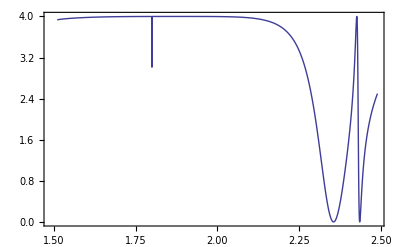

```mathematica
ListPlot[Transpose[{Earray,Table[Smat[[i]][[1,1]]*Smat[[i]][[1,1]],{i,1,NumE}]}],Joined->True,PlotTheme->None,Frame->True]
```

### scratch work

Part::partd: Part specification threechan2bsplusparity⟦2⟧ is longer than depth of object.

Part::partd: Part specification threechan2bsnegparity⟦2⟧ is longer than depth of object.

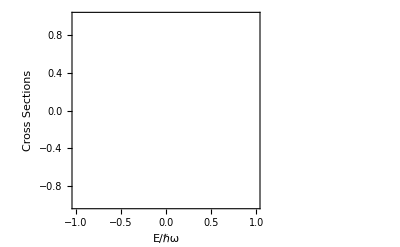

```mathematica
ptwochan=ListPlot[Join[{threechan2bsplusparity[[2]]},{threechan2bsnegparity[[2]]}],FrameLabel->{"E/ℏω","Cross Sections"},LabelStyle->{Black,18},Frame->True,PlotTheme->None,PlotStyle->{{Black},{Red,Dashed},{Green},{Blue}},Joined->True,Epilog->{
Style[Text["σ_(2⟵1)^(Π = +1)",{1.64,0.037}],{Black,18}],Style[Text["σ_(2⟵1)^(Π = -1)",{1.65,0.02}],{Red,18}]}]
```

```mathematica
TotalInelastic12=Transpose[{twochan2bsplusparity[[1,1]]}]
```

```mathematica
rawcurves=Import["/Users/niravmehta/Documents/GitHub/AtomIon1D/QuickEffV.dat"];
```

```mathematica
Dimensions[rawcurves][[2]]
```

9

```mathematica
Transpose[rawcurves][[2]];
```

```mathematica
U1Dat=Transpose[{Transpose[rawcurves][[1]],Transpose[rawcurves][[2]]}];
```

```mathematica
Dimensions[rawcurves]
```

{1000,13}

```mathematica
rawcurves[[1]]
```

{50.,0.499992,1.49999,2.5,3.50001,4.50002,5.50005,6.50008,7.50012,36.5154,37.5167,38.0833,39.062}

```mathematica
U1[x_]:=Interpolation[U1Dat][x]
```

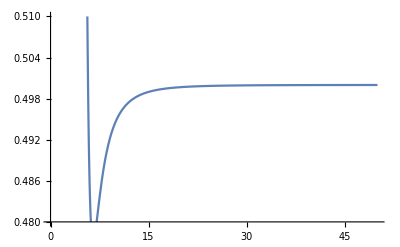

```mathematica
Plot[U1[x],{x,.75,50},PlotRange->{0.48,.51}]
```

For the even states:

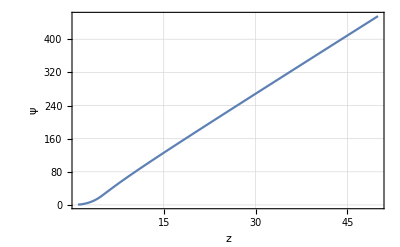

```mathematica
Clear[ψ];ϵ=0.5;ψ=ψ/.NDSolve[{-1/(2 μ)ψ''[z]+U1[z] ψ[z]==ϵ ψ[z],ψ[1]==1,ψ'[1]==0},ψ,{z,0.75,50}][[1]];
Plot[ψ[z],{z,1,50},Frame->True,GridLines->Automatic,LabelStyle->Large,FrameLabel->{"z","ψ"}]
```

```mathematica
Solve[{A u1==Sin[k x1]+TanDelta Cos[k x1],A u2==Sin[k x2]+TanDelta Cos[k x2]},{A,TanDelta}]//Simplify
```

{{A→-Sin[k (x1-x2)]/(u2 Cos[k x1]-u1 Cos[k x2]),TanDelta→(-u2 Sin[k x1]+u1 Sin[k x2])/(u2 Cos[k x1]-u1 Cos[k x2])}}

```mathematica
CalcTanDelta[Εtest_,xmax_,xmin_,μ_,V_]:=
Module[{TanDelta,sol,k,u1,u2,x1,x2,u},
x1=0.95 xmax;
x2=0.99xmax;
k=√(2 μ Εtest);
sol=NDSolve[{-1/(2 μ)u''[x]+V[x] u[x]==Εtest u[x],u[xmin]==0.001,u'[xmin]==0},u,{x,xmin,xmax}];
u1=u[x1]/.sol[[1]];
u2=u[x2]/.sol[[1]];
TanDelta=(-u2 Sin[k x1]+u1 Sin[k x2])/(u2 Cos[k x1]-u1 Cos[k x2]);
Return[TanDelta]
]
```

```mathematica
CalcERE[xmin_,xmax_,ΕMin_,ΕMax_,μ_,V_,NumE_]:=
Module[{EREData,ascat,reff,A,B,fitpars,dE,ksqr,adata},
dE=(ΕMax-ΕMin)/NumE;
EREData=Table[{2μ Εtest,√(2μ Εtest)/CalcTanDelta[Εtest,xmax,xmin,μ,V]},{Εtest,ΕMin,ΕMax,dE}];
adata=Table[{Εtest,-CalcTanDelta[Εtest,xmax,xmin,μ,V]/(√(2μ Εtest))},{Εtest,ΕMin,ΕMax,dE}];
fitpars=FindFit[EREData,A+B ksqr,{A,B},ksqr];
ascat=-1/A/.fitpars;
reff=2B/.fitpars;
Return[{ascat,reff,EREData,adata}]
]
```

```mathematica
Urel[x]=U1[x]-0.5
```

-0.5+InterpolatingFunction[…][x]

```mathematica
kcotdel=CalcERE[.75,50.0,0.01,0.99,μ,Urel,100];
```

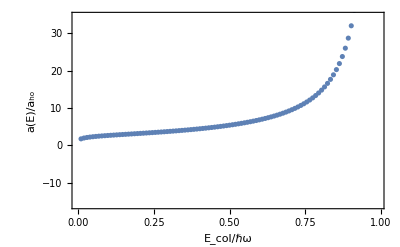

```mathematica
pMathematica1chan=ListPlot[kcotdel[[4]],Frame->True,FrameLabel->{"E_col/ℏω","a(E)/a_ho"}]
```

```mathematica
CABA12chan=Import["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/Observables.dat"];
CABA12chan=Transpose[Drop[Transpose[CABA12chan],{3,4}]];
```

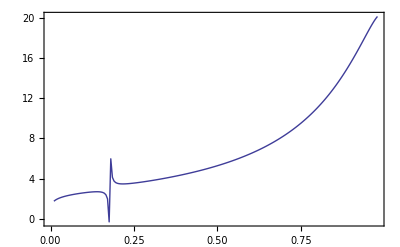

```mathematica
ListPlot[CABA12chan,Joined->True,PlotTheme->None,Frame->True]
```

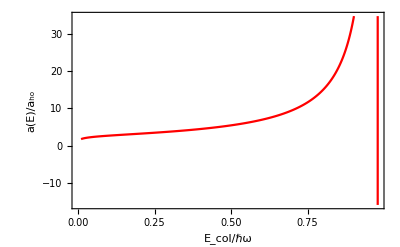

```mathematica
pcaba1chan=ListPlot[CABA1chan,Frame->True,FrameLabel->{"E_col/ℏω","a(E)/a_ho"},Joined->True,PlotStyle->Red]
```

```mathematica
CABA6chan=Import["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/CABA1BS-6chan.dat"];
CABA6chan=Transpose[Drop[Transpose[CABA6chan],{3}]];
```

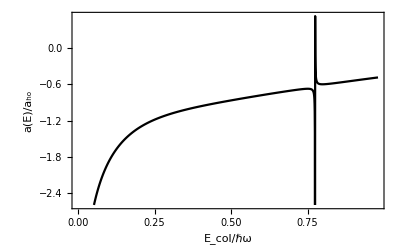

```mathematica
pcaba6chan=ListPlot[CABA6chan,Frame->True,FrameLabel->{"E_col/ℏω","a(E)/a_ho"},Joined->True,PlotStyle->Black]
```

```mathematica
Show[pcaba6chan,pMathematica1chan]
```

-Graphics-

```mathematica
Cos[π-α]
```

-Cos[α]

```mathematica
1/Tan[θc]
```

5.33083

```mathematica
1.07*3400
```

3638.

```mathematica
TrigExpand[Cos[a+b]]
```

Cos[a] Cos[b]-Sin[a] Sin[b]

```mathematica
Cos[π-ϕ]
```

-Cos[ϕ]

```mathematica
Sin[π-ϕ]
```

Sin[ϕ]

```mathematica
3645/3400.
```

1.07206

```mathematica
GegenbauerC[λ,0,x]
```

0

```mathematica
-2!!
```

-2

## Bound states

Let’s take a look at the bound states that live in the quadratic potential curves to see if they line up with the resonances.

```mathematica
EffVData=Transpose[Import["/Users/niravmehta/Documents/GitHub/AtomIon1D/QuickEffV.dat"]];
```

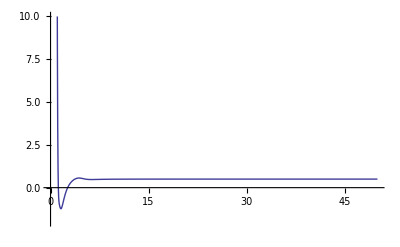

```mathematica
ListPlot[Transpose[{EffVData[[1]],EffVData[[2]]}],Joined->True,PlotRange->{-2,10},PlotTheme->None]
```

```mathematica
RawP
```

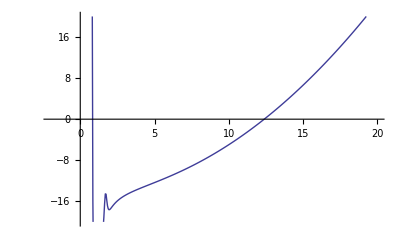

```mathematica
ListPlot[Transpose[{EffVData[[1]],EffVData[[8]]}],Joined->True,PlotRange->{{-2,20},{-20,20}},PlotTheme->None]
```

```mathematica
VeffBound1=Interpolation[Transpose[{EffVData[[1]],EffVData[[8]]}]]
```

InterpolatingFunction[…]

```mathematica
VeffBound2=Interpolation[Transpose[{EffVData[[1]],EffVData[[9]]}]]
```

InterpolatingFunction[…]

```mathematica
{vals,vecs}=NDEigensystem[{-1/(2μ)F''[R]+(VeffBound1[R]+200)F[R],DirichletCondition[F[R]==0,True]},F[R],{R,0.75,40},20,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->.1}}}];
```

```mathematica
vals-200
```

{-15.9619,-12.0011,-9.50558,-7.20881,-4.99077,-2.81563,-0.668014,1.46008,3.57336,5.67484,7.76656,9.85002,11.9263,13.9963,16.0608,18.1204,20.1757,22.227,24.2746,26.3188}

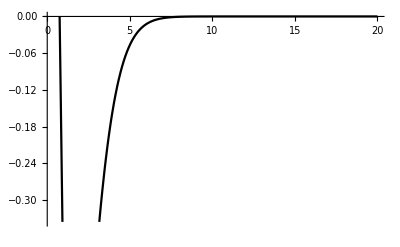

```mathematica
Plot[vecs[[1]],{R,0.2,20}]
```

```mathematica
{vals,vecs}=NDEigensystem[{(-1/(2μ)F''[R]+(VeffBound2[R]+200)F[R]),DirichletCondition[F[R]==0,True]},F[R],{R,0.5,40},20];
```

```mathematica
vals-200
```

{-13.4342,-11.0655,-8.81239,-6.48795,-3.96052,-1.49481,0.528831,3.41553,5.80493,8.56718,11.212,14.0609,16.6995,19.7561,22.2382,25.3293,27.9201,30.7471,34.1176,36.3081}

InterpolatingFunction::dmval: Input value {0.301015} lies outside the range of data in the interpolating function. Extrapolation will be used.

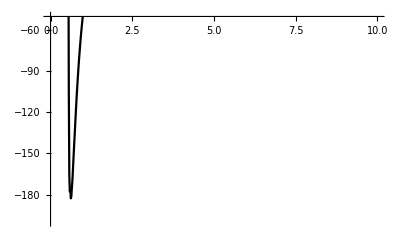

```mathematica
Plot[VeffBound2[R],{R,0.3,50},PlotRange->{{0,10},{-200,-50}}]
```

```mathematica
{vals,vecs}=Eigensystem[{{1.1,2.2,3.25},{0.76,4.6,5},{0.1,0.1,6.1}}]
```

{{6.60674,4.52536,0.667901},{{0.48687,0.833694,0.260598},{-0.479424,-0.873368,0.085911},{0.985096,-0.171352,-0.0149803}}}

```mathematica
vecs//MatrixForm
```

(0.48687 | 0.833694 | 0.260598
-0.479424 | -0.873368 | 0.085911
0.985096 | -0.171352 | -0.0149803)

```mathematica
1/1.4603
```

0.684791